```mathematica
Smac=((ρon-ρoff)σon σoff)/((σon+σoff)(e+σon+σoff))Log[ρon/ρoff];
```

```mathematica
Smac2=Smac/.{ρon->B σoff}//FullSimplify
```

(σoff (-ρoff+B σoff) σon Log[(B σoff)/ρoff])/((σoff+σon) (e+σoff+σon))

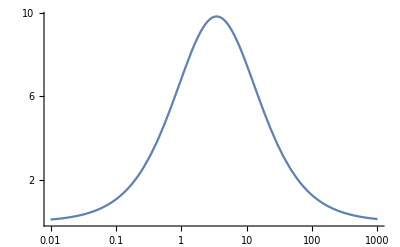

```mathematica
Plot[Smac2/.{B->10/3,σoff->3,e->1,ρoff->0.1},{σon,10^-2,10^3},ScalingFunctions->{"Log","Linear"}]
```

```mathematica
σontab=Table[{σon,Smac2}/.{B->10/3,σoff->3,e->1,ρoff->0.1,σon->10^x},{x,-2,3,0.1}]
```

{{0.01,0.113316},{0.0125893,0.142442},{0.0158489,0.178984},{0.0199526,0.224792},{0.0251189,0.282151},{0.0316228,0.353873},{0.0398107,0.443399},{0.0501187,0.554904},{0.0630957,0.693401},{0.0794328,0.864832},{0.1,1.07611},{0.125893,1.33509},{0.158489,1.65039},{0.199526,2.03103},{0.251189,2.48571},{0.316228,3.02171},{0.398107,3.64334},{0.501187,4.3497},{0.630957,5.13228},{0.794328,5.97227},{1.,6.83868},{1.25893,7.68785},{1.58489,8.46561},{1.99526,9.11246},{2.51189,9.57183},{3.16228,9.79963},{3.98107,9.7728},{5.01187,9.49408},{6.30957,8.99149},{7.94328,8.31248},{10.,7.51503},{12.5893,6.65809},{15.8489,5.794},{19.9526,4.96383},{25.1189,4.19595},{31.6228,3.50681},{39.8107,2.90315},{50.1187,2.38455},{63.0957,1.94596},{79.4328,1.57967},{100.,1.27683},{125.893,1.02847},{158.489,0.826102},{199.526,0.662065},{251.189,0.529645},{316.228,0.423099},{398.107,0.337598},{501.187,0.269127},{630.957,0.214387},{794.328,0.17068},{1000.,0.135821}}

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\sigma-on-tab.csv",σontab,"CSV"]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\sigma-on-tab.csv

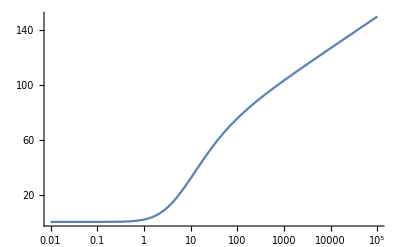

```mathematica
Plot[Smac2/.{B->10/3,σon->3,e->1,ρoff->0.1},{σoff,10^-2,10^5},ScalingFunctions->{"Log","Linear"},PlotRange->All]
```

```mathematica
σofftab=Table[{σoff,Smac2}/.{B->10/3,σon->3,e->1,ρoff->0.1,σoff->10^x},{x,-2,5,0.1}]
```

{{0.01,0.000182039},{0.0125893,0.000157452},{0.0158489,0.000118165},{0.0199526,0.000067347},{0.0251189,0.0000178809},{0.0316228,2.21183×10^-6},{0.0398107,0.0000899882},{0.0501187,0.00041889},{0.0630957,0.00124741},{0.0794328,0.00304352},{0.1,0.00663085},{0.125893,0.0134249},{0.158489,0.0258067},{0.199526,0.0476983},{0.251189,0.0854222},{0.316228,0.148937},{0.398107,0.253525},{0.501187,0.42194},{0.630957,0.68689},{0.794328,1.09345},{1.,1.70068},{1.25893,2.58125},{1.58489,3.81792},{1.99526,5.49576},{2.51189,7.69028},{3.16228,10.4533},{3.98107,13.7998},{5.01187,17.7001},{6.30957,22.0801},{7.94328,26.8307},{10.,31.8226},{12.5893,36.9237},{15.8489,42.0143},{19.9526,46.9969},{25.1189,51.8007},{31.6228,56.3812},{39.8107,60.717},{50.1187,64.8044},{63.0957,68.6523},{79.4328,72.278},{100.,75.7029},{125.893,78.9503},{158.489,82.0434},{199.526,85.004},{251.189,87.8519},{316.228,90.6049},{398.107,93.2784},{501.187,95.8858},{630.957,98.4382},{794.328,100.945},{1000.,103.415},{1258.93,105.854},{1584.89,108.268},{1995.26,110.661},{2511.89,113.037},{3162.28,115.399},{3981.07,117.751},{5011.87,120.093},{6309.57,122.427},{7943.28,124.756},{10000.,127.08},{12589.3,129.399},{15848.9,131.716},{19952.6,134.03},{25118.9,136.341},{31622.8,138.651},{39810.7,140.96},{50118.7,143.267},{63095.7,145.573},{79432.8,147.879},{100000.,150.184}}

```mathematica
ListPlot[σofftab,ScalingFunctions->{"Log","Linear"}];
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\sigma-off-tab.csv",σofftab,"CSV"]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\sigma-off-tab.csv

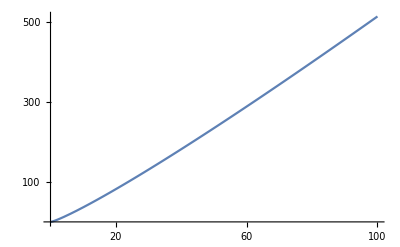

```mathematica
Plot[Smac2/.{σoff->3,σon->3,e->1,ρoff->0.1},{B,10^-2,10^2},ScalingFunctions->{"Linear","Linear"}]
```

```mathematica
Btab=Table[{B,Smac2}/.{σoff->3,σon->3,e->1,ρoff->0.1},{B,1,100,1}];
```

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\B-tab.csv",Btab,"CSV"]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\B-tab.csv

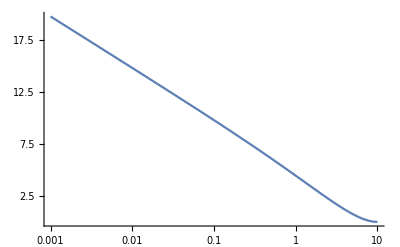

```mathematica
Plot[Smac2/.{σoff->3,σon->3,e->1,B->10/3},{ρoff,10^-3,10^1},ScalingFunctions->{"Log","Linear"}]
```

```mathematica
ρofftab=Table[{ρoff,Smac2}/.{σoff->3,σon->3,e->1,B->10/3,ρoff->10^x},{x,-3,1,0.1}]
```

{{0.001,19.7345},{0.00125893,19.2406},{0.00158489,18.7466},{0.00199526,18.2526},{0.00251189,17.7583},{0.00316228,17.2639},{0.00398107,16.7693},{0.00501187,16.2744},{0.00630957,15.7792},{0.00794328,15.2836},{0.01,14.7875},{0.0125893,14.2909},{0.0158489,13.7936},{0.0199526,13.2955},{0.0251189,12.7965},{0.0316228,12.2963},{0.0398107,11.7947},{0.0501187,11.2916},{0.0630957,10.7866},{0.0794328,10.2793},{0.1,9.76954},{0.125893,9.25679},{0.158489,8.74064},{0.199526,8.22063},{0.251189,7.69627},{0.316228,7.16712},{0.398107,6.63275},{0.501187,6.09287},{0.630957,5.54735},{0.794328,4.9964},{1.,4.4407},{1.25893,3.88165},{1.58489,3.32169},{1.99526,2.76474},{2.51189,2.21683},{3.16228,1.6869},{3.98107,1.18792},{5.01187,0.738359},{6.30957,0.364179},{7.94328,0.101481},{10.,0.}}

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\rho-off-tab.csv",ρofftab,"CSV"]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\rho-off-tab.csv

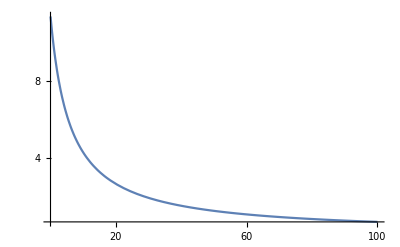

```mathematica
Plot[Smac2/.{σoff->3,σon->3,ρoff->1/10,B->10/3},{e,10^-2,10^2},ScalingFunctions->{"Linear","Linear"},PlotRange->All]
```

```mathematica
etab=Table[{e,Smac2}/.{σoff->3,σon->3,ρoff->1/10,B->10/3,e->10^x},{x,-2,2,0.1}]
```

{{0.01,11.3788},{0.0125893,11.3739},{0.0158489,11.3678},{0.0199526,11.36},{0.0251189,11.3503},{0.0316228,11.338},{0.0398107,11.3227},{0.0501187,11.3034},{0.0630957,11.2792},{0.0794328,11.2489},{0.1,11.2109},{0.125893,11.1636},{0.158489,11.1045},{0.199526,11.031},{0.251189,10.9398},{0.316228,10.8272},{0.398107,10.6886},{0.501187,10.5191},{0.630957,10.3133},{0.794328,10.0653},{1.,9.76954},{1.25893,9.42106},{1.58489,9.01618},{1.99526,8.55341},{2.51189,8.03427},{3.16228,7.46395},{3.98107,6.85165},{5.01187,6.21028},{6.30957,5.55558},{7.94328,4.90464},{10.,4.27417},{12.5893,3.67883},{15.8489,3.12998},{19.9526,2.63506},{25.1189,2.1976},{31.6228,1.8177},{39.8107,1.49281},{50.1187,1.21861},{63.0957,0.989739},{79.4328,0.800474},{100.,0.645158}}

```mathematica
Export["\\\\wsl.localhost\\Ubuntu\\home\\jamesh\\GitHub\\thermo-gene-expression\\e-tab.csv",etab,"CSV"]
```

\\wsl.localhost\Ubuntu\home\jamesh\GitHub\thermo-gene-expression\e-tab.csv